```mathematica
m:=20000;V:=10;g:=9.8;p:=1000;v0:=-10;k:=5000;H0:=100;a=25;p0=250000;H1=90;c=m*g-p*g*V
```

98000.

```mathematica
Simplify[DSolve[{m*y'[t]==-(c-k*y[t]),y[0]==v0},y[t],t]]
```

{{y[t]→19.6-29.6 ⅇ^(-0.25 t)}}

```mathematica
A:=-2
```

```mathematica
vb[t_]=(A+1)E^(-t)-A
```

2-ⅇ^-t

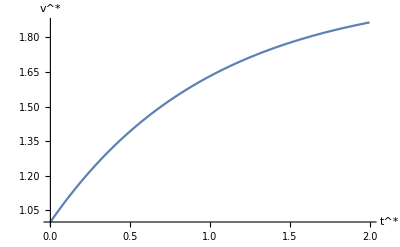

```mathematica
Plot[vb[t],{t,0,2},AxesLabel->{SuperStar[t],SuperStar[v]}]
```

```mathematica
A:=100;B:=0
```

```mathematica
Hb[v_]:=A(v-1)+1-A*B*Log[(B+v)/(B+1)]
```

```mathematica
FullSimplify[Hb[v]]
```

-99+100 v

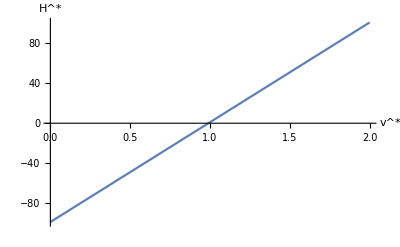

```mathematica
Plot[Hb[v],{v,0,2},AxesLabel->{SuperStar[v],SuperStar[H]}]
```

```mathematica
Q:=2;
```

```mathematica
vv[t_]:=(1-Q)*E^t+Q*E^(-t);
```

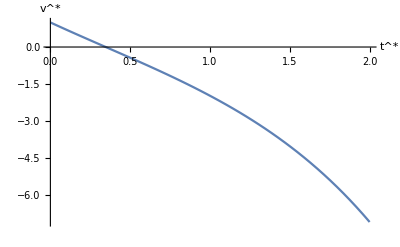

```mathematica
Plot[vv[t],{t,0,2},AxesLabel->{SuperStar[t],SuperStar[v]}]
```

```mathematica
P:=10;L:=4;
```

```mathematica
h[t_]:=(P+L)(E^(-t)-1)+P*t+1
```

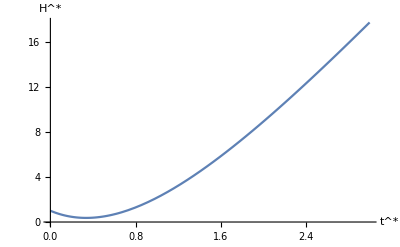

```mathematica
Plot[h[t],{t,0,3},AxesLabel->{SuperStar[t],SuperStar[H]}]
```

```mathematica
w:=-15;u:=-12;r:=28;
```

```mathematica
HH[t_]:=w*E^t+u*E^(-t)+r;
```

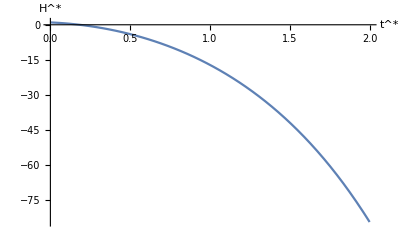

```mathematica
Plot[HH[t],{t,0,2},AxesLabel->{SuperStar[t],SuperStar[H]}]
```

```mathematica
A:=0.5;B:=0;
```

```mathematica
hh[v_]:=A Log[Abs[(B+v^2)/(B+1)]]+1
```

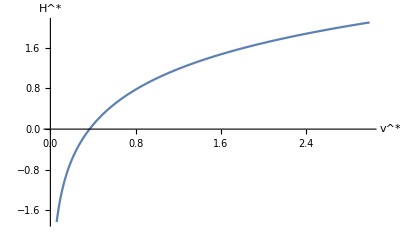

```mathematica
Plot[hh[v],{v,0,3},AxesLabel->{SuperStar[v],SuperStar[H]}]
```

```mathematica
w:=-(3)^(1/2)/3;e:=-(Pi/3+1/2);
```

```mathematica
vi[t_]:=w*Tan[t/2+e]
```

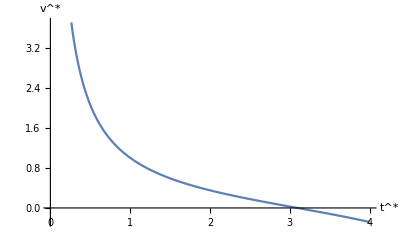

```mathematica
Plot[vi[t],{t,0,4},AxesLabel->{SuperStar[t],SuperStar[v]}]
```

```mathematica
l:=-0.5;
vqw[t_]:=2l(l+1)/(l+1+(l-1)E^t)-l
```

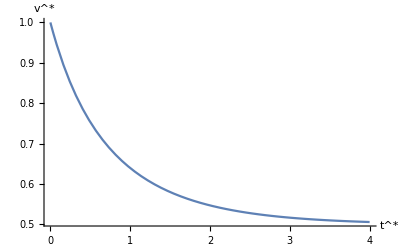

```mathematica
Plot[vqw[t],{t,0,4},AxesLabel->{SuperStar[t],SuperStar[v]}]
```

```mathematica
lam:=25;
```

```mathematica
vlottt[t_]:=-1/(lam*t-1)
```

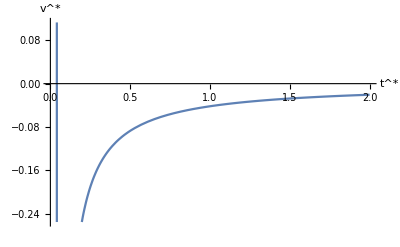

```mathematica
Plot[vlottt[t],{t,0,2},AxesLabel->{SuperStar[t],SuperStar[v]}]
```

```mathematica
A:=20;B:=-0.2
```

```mathematica
H[t_]:=A Log[1-B*t]+1
```

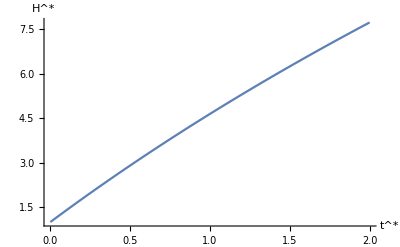

```mathematica
Plot[H[t],{t,0,2},AxesLabel->{SuperStar[t],SuperStar[H]}]
```

```mathematica
A:=20;B:=-2;
H[t_]:=1/2*A*t-A*Log[((1-B)E^t+1+B)/2]+1
```

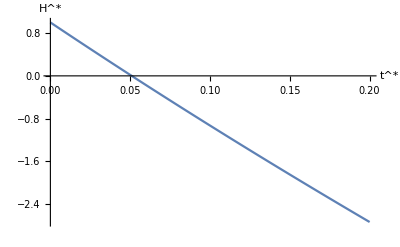

```mathematica
Plot[H[t],{t,0,0.2},AxesLabel->{SuperStar[t],SuperStar[H]}]
```

```mathematica
A:=-0.50;B:=0.50;d:=0.20;
```

```mathematica
v[h_]:=(-A-B*h+(1+A+B)E^(d(h-1)))^(1/2)
```

```mathematica
v[h]
```

√(0.5+1. ⅇ^(0.2 (-1+h))-0.5 h)

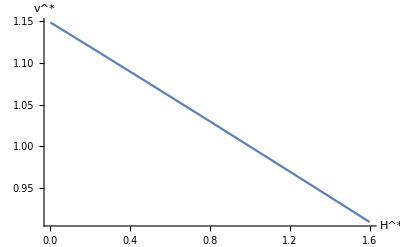

```mathematica
Plot[v[h],{h,0,1.6},AxesLabel->{SuperStar[H],SuperStar[v]}]
```